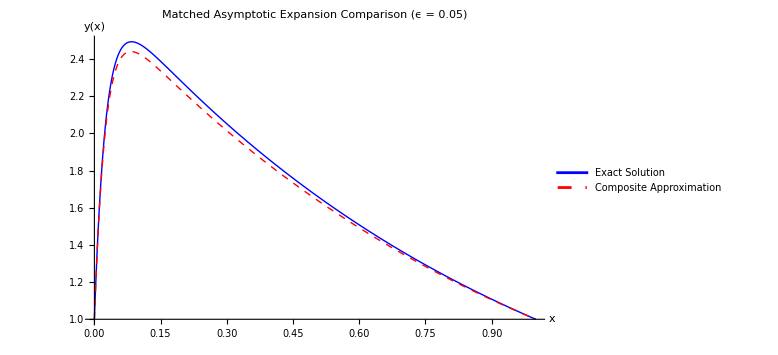

```mathematica
ClearAll[r1,r2,yExact,yComp];

(*Define the roots of the characteristic equation*)
r1[eps_]:=(-1+Sqrt[1-2*eps])/eps;
r2[eps_]:=(-1-Sqrt[1-2*eps])/eps;

(*Define the Exact Solution*)
yExact[x_,eps_]:=((1-Exp[r2[eps]])/(Exp[r1[eps]]-Exp[r2[eps]]))*Exp[r1[eps]*x]+((Exp[r1[eps]]-1)/(Exp[r1[eps]]-Exp[r2[eps]]))*Exp[r2[eps]*x];

(*Define the Composite Approximate Solution*)
yComp[x_,eps_]:=Exp[1-x]+(1-Exp[1])*Exp[-2*x/eps];

(*1. Static Plot for a fixed epsilon*)
epsVal=0.05;
Plot[{yExact[x,epsVal],yComp[x,epsVal]},{x,0,1},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"Exact Solution","Composite Approximation"},AxesLabel->{"x","y(x)"},PlotLabel->Row[{"Matched Asymptotic Expansion Comparison (ϵ = ",epsVal,")"}],PlotRange->All,ImageSize->Large]

(*2. Interactive Plot using Manipulate*)
Plot[{yExact[x,eps],yComp[x,eps]},{x,0,1},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"Exact Solution","Composite Approximation"},AxesLabel->{"x","y(x)"},PlotLabel->Row[{"Boundary Layer Behavior at x=0"}],PlotRange->All,ImageSize->Large],{{eps,0.1,"ϵ (Perturbation Parameter)"},0.01,0.49,0.01,Appearance->"Labeled"}
```